## Handle-slide & Homotopy Calculator

This code is designed to be able to draw representatives of morphisms in the band category in a “square with bands” model with all the bands isolated on the right hand edge. It is also designed to perform the two necessary topological moves on said pictures being 
(a) handle-slides: this is where we slide one band over another band and track what happens to embedded curves,
(b) homotopy: this is where we can smoothly deform the embedded curves on the surface. We note that the notion of homotopy employed here is as simple as possible - i.e. we want to remove redundant interactions of curves with bands by “pulling strings tight”, e.g. the picture:

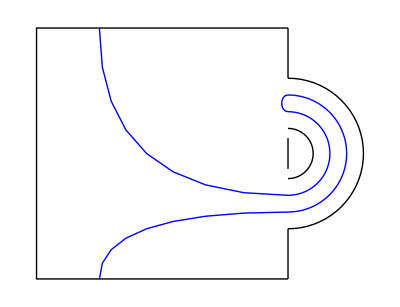
-Graphics-1

```mathematica
Hompic[{1,1,1,1,{{0,1,2,2}},{{{0,1},{1,1}},{{2,2},{2,1}},{{1,2},{3,1}}}}]
```

Should be best represented as:

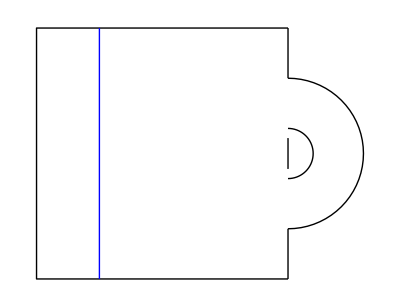
-Graphics-1

```mathematica
Hompic[Htpe[{1,1,1,1,{{0,1,2,2}},{{{0,1},{1,1}},{{2,2},{2,1}},{{1,2},{3,1}}}}]]
```

In order to encode these kinds of pictures and operations, we need to understand these pictures as some combinatorial data. The idea is we have a complex list which I will denote

“{sc , N , M , n , BD , CD}”

which encodes all the data of a picture. Let me try and explain each entry of this list 

- sc: This is a scalar factor for the picture. I have included this to make it easier to track the number of times we remove a loop. It will be more useful for future extensions where I include composition
- N: Number of marked points on the bottom edge of the picture
- M: Number of marked points on the top edge of the picture 
- n: Number of bands on the right hand edge
- BD: BD stands for band data. BD is itself a list of the n bands included in a picture, where a band is a list of 4 values “{ tw , i , j , k }”. tw here is the twist parameter; 0 for untwisted, 1 for twisted. i and j are the positions at which the band joins, the code should work symmetrically in i and j. k number of embedded lines passing through the band. 

I will explain the last entry CD soon, however, let me first illustrate how this works. Say we want to draw a a morphism from 1 → 1 which is represented pair of overlapping bands with one of the bands being twisted and one being untwisted. Then we would specify the list above as {sc , 1 , 1 , 2 , {{0,1,3,1},{1,2,4,3}},CD}. We keep sc arbitrary for now, although we can set it to 1 for convenience. Here we specified n=2 for two bands and BD={{0,1,3,1},{1,2,4,3}} tells us what both bands should look like e.g. {0,1,3,1} is an untwisted band (tw=0) joining the bottom most position to the 3rd from the bottom, which has 1 embedded line passing through it. 

We draw this picture with the Hompic function where our data above is the input (we will write CD as an empty list {} for now):

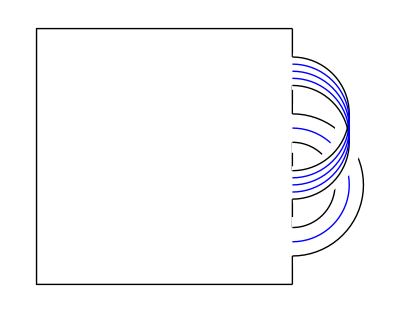
-Graphics-sc

```mathematica
Hompic[{sc,1,1,2,{{0,1,3,1},{1,2,4,3}},{}}]
```

This looks alright so far (I have added some additional lines through the bands for example). We can see that to turn this into an actual morphism however with embedded curves that have the marked points as boundaries we need to add more lines to our picture - we can view this as a problem of connecting certain points to one another. This is the role of the entry CD which stands for connection data. CD is again itself a list which encodes all the connections needed to turn this into a complete picture.

Say for example we want the line which comes from the bottom marked point to enter the untwisted band at the bottom position. if we let 0 be the “row” which the bottom points belong to and 1 be the “row” which the points in the bottom position belong to then we can say we want to join the first (of one) point the 0th row to the first point in the 1st row. To do this we would add the entry {{0 , 1} , {1 , 1}} to the list CD.

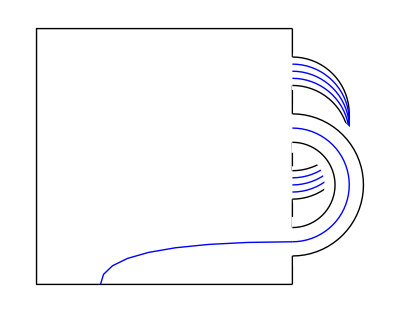
-Graphics-sc

```mathematica
Hompic[{sc,1,1,2,{{1,2,4,3},{0,1,3,1}},{{{0,1},{1,1}}}}]
```

This is one of many connections needed to complete the picture - in general an entry of the list CD should be of the form {{i,l},{j,m}} - this connects the l-th point in the i-th “row” to the m-th point in the j-th “row”. Where we always read bottom to top or left to right (whichever makes sense). Note than in a picture with n-bands the row value should not exceed 2n+1 - this corresponds to marked points on the top edge. For example we can complete the above picture as:

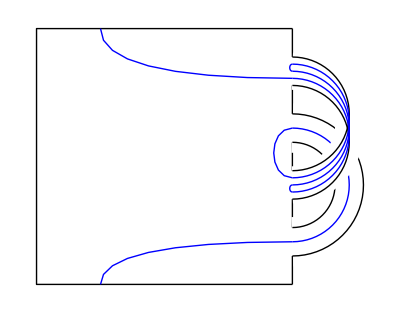
-Graphics-sc

```mathematica
Hompic[{sc,1,1,2,{{0,1,3,1},{1,2,4,3}},
{ 
{{0,1},{1,1}},
{{3,1},{2,3}},
{{4,3},{4,2}},
{{2,2},{2,1}},
{{4,1},{5,1}}
}}]
```

The code should be set up so that any valid picture you draw using this input format should have crossingless embedded lines - let me know if you find a counter example! 

NOTE: one of the key assumptions this model to draw surfaces is using is that essentially the bands have 0 length so a line either propagates fully through a band, or not at all. It cannot propagate halfway down a line and then turn back. This should be topologically insignificant.

Now we can get to the main ideas - Now that we have encoded our pictures as combinatorial data we can define the topological moves algorithmically. 

Firstly the homotopy move - this detects redundant interactions a curve has with a band and straightens them out. To do this we use the function “Htpe” and input the data of the picture in list form, the output is the data of another picture in list form which we then need to draw. For example, if we apply this to the picture we have above this yields:

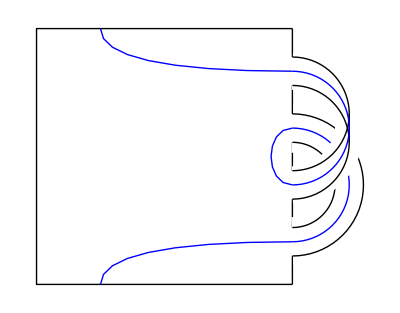
-Graphics-sc

```mathematica
ex1Data=Htpe[{sc,1,1,2,{{0,1,3,1},{1,2,4,3}},
{ 
{{0,1},{1,1}},
{{3,1},{2,3}},
{{4,3},{4,2}},
{{2,2},{2,1}},
{{4,1},{5,1}}
}}];
Hompic[ex1Data]
```

The second move we want to encode algorithmically is handle-sliding. To do this we use the function “Hslide[i,dir]” as an operator to apply to the data of a picture - here the inputs tell you to move the band in the direction dir (“u” or “up” for up, “d” or “down” for down) at the i-th position. The output is again the data of a picture in list form so we need to use Hompic to draw it. For example, let us slide the band down at the third position (i.e. sliding the untwisted band along the twisted band to give two twisted bands). To do this we write

{sc,1,1,2,{{1,2,3,2},{1,4,1,1}},{{{0,1},{1,1}},{{3,1},{5,1}},{{2,1},{2,2}},{{4,1},{3,2}}}}

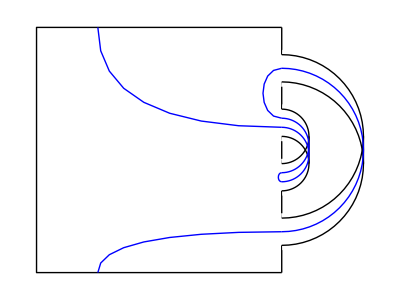
-Graphics-sc

```mathematica
ex2Data=Hslide[3,"d"][ex1Data];
ex2Data
Hompic[ex2Data]
```

```mathematica
{sc,1,1,2,{{1,2,3,2},{1,4,1,1}},{{{0,1},{1,1}},{{3,1},{5,1}},{{2,1},{2,2}},{{4,1},{3,2}}}}
```

{sc,1,1,2,{{1,2,3,2},{1,4,1,1}},{{{0,1},{1,1}},{{3,1},{5,1}},{{2,1},{2,2}},{{4,1},{3,2}}}}

and lets finish it off by homotoping!

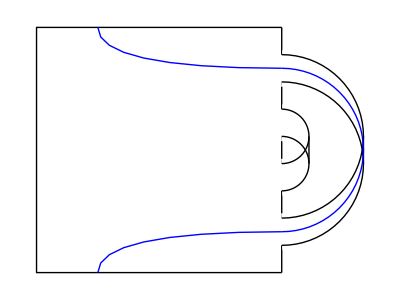
-Graphics-sc

```mathematica
Hompic[Htpe[ex2Data]]
```

With the Htpe and Hslide operations defined now, it is not too difficult to imagine writing a function which tries to find an optimal representative for a given picture so I think this should definitely be a future extension.

NOTE: So far I haven’t really added a mechanism for removing closed curves (especially ones with non-trivial homotopy classes). The Htpe function will remove contractible closed curves in the simple situation below:

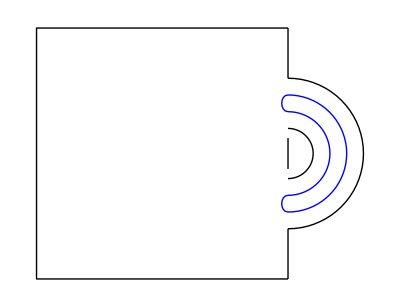
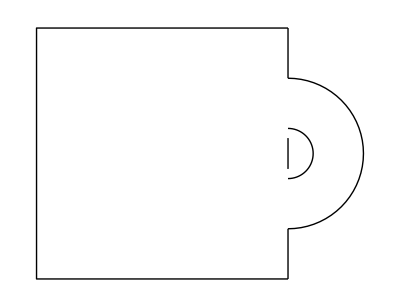
-Graphics-1==-Graphics-α

```mathematica
Hompic[{1,0,0,1,{{0,1,2,2}},{{{1,1},{1,2}},{{2,1},{2,2}}}}]==Hompic[Htpe[{1,0,0,1,{{0,1,2,2}},{{{1,1},{1,2}},{{2,1},{2,2}}}}]]
```

where I have Globally specified the Loop parameter as δ.

I have fairly well tested the code below it should work ok provided the data is input in the way I have described and a picture is valid. However, as you can probably tell this is really quite fiddly so it is entirely possible there are errors/oversights so please let me know if you are able to find any bugs or if you think a topological move has been performed incorrectly by this program! I have drawn some sample pictures and examples below which you can run to get a feel for the code. Hope you enjoy the program :) .

```mathematica
"Globally Specify 2-sided Loop Parameter as α";
LP2s=α;
"Globally Specify 1-sided Loop Parameter as β";
LP1s=β;
```

```mathematica
Base[n_]:=Flatten[{Table[Line[{{0,2*i},{0,2*i+1}}],{i,0,2*n}],{Line[{{0,0},{-4*n-1,0},{-4*n-1,4*n+1},{0,4*n+1}}]}}]
```

```mathematica
band[n_,{t_,i_,j_,k_}]:=If[t==0,
Module[{r1,r2,c},
r1=Abs[(2*j+1-2*i)/2];
r2=Abs[(2*j-1-2*i)/2];
c=Min[2*i-1,2*j-1]+Max[r1,r2];
Flatten[{White,Thickness[0.2/((4*n+1)/4)],Circle[{0,c},(r1+r2)/2,{-π/2,π/2}],
Black,AbsoluteThickness[1],Circle[{0,c},r1,{-π/2,π/2}],
Circle[{0,c},r2,{-π/2,π/2}],
Blue,Table[Circle[{0,c},Min[r1,r2]+l*Abs[r1-r2]/(k+1),{-π/2,π/2}],{l,1,k}],Black}]
],
Module[{r,c1,c2},
r=Abs[(i-j)];
c1=Min[2*i-1,2*j-1]+r;
c2=Min[2*i,2*j]+r;
Flatten[{White,Thickness[0.1/n],
Circle[{0,c1+1/3},r,{-π/2,π/2}],
Circle[{0,c1+2/3},r,{-π/2,π/2}],
Black,AbsoluteThickness[1],Line[{{r,c1},{r,c2}}],
Circle[{0,c1},r,{-π/2,π/2}],
Circle[{0,c2},r,{-π/2,π/2}],Blue,
Table[Circle[{0,c1+l/(k+1)},r,{-π/2,π/2}],{l,1,k}],Black}]
]]
eband[n_,{t_,i_,j_,k_}]:=If[t==0,
Module[{r1,r2,c},
r1=Abs[(2*j+1-2*i)/2];
r2=Abs[(2*j-1-2*i)/2];
c=Min[2*i-1,2*j-1]+Max[r1,r2];
Flatten[{White,Thickness[0.2/((4*n+1)/4)],Circle[{0,c},(r1+r2)/2,{-π/2,π/2}],
Black,AbsoluteThickness[1],Circle[{0,c},r1,{-π/2,π/2}],
Circle[{0,c},r2,{-π/2,π/2}],Black}]
],
Module[{r,c1,c2},
r=Abs[(i-j)];
c1=Min[2*i-1,2*j-1]+r;
c2=Min[2*i,2*j]+r;
Flatten[{White,Thickness[0.1/n],
Circle[{0,c1+1/3},r,{-π/2,π/2}],
Circle[{0,c1+2/3},r,{-π/2,π/2}],
Black,AbsoluteThickness[1],Line[{{r,c1},{r,c2}}],
Circle[{0,c1},r,{-π/2,π/2}],
Circle[{0,c2},r,{-π/2,π/2}],Black}]
]]
```

```mathematica
connect[N_,M_,n_,{{i1_,m1_,k1_},{i2_,m2_,k2_}}]:=
Module[{h1,h2,l10,l20,l12,l22,d0,r1,c1,d2,c0,c2,r0,r2},
h1=2*i1-1+m1/(k1+1);
h2=2*i2-1+m2/(k2+1);
l10=-4*n-1+0.5*m1/(N+1)*(4*n+1);
l20=-4*n-1+0.5*m2/(N+1)*(4*n+1);
l12=-4*n-1+0.5*m1/(M+1)*(4*n+1);
l22=-4*n-1+0.5*m2/(M+1)*(4*n+1);
r1=Abs[((2*i1+1+m1/(k1+1))-(2*i2+1+m2/(k2+1)))/2];
r0=(Abs[l10-l20])/2;
r2=(Abs[l12-l22])/2;;
d0=Abs[m1-m2]/(N+1);
d2=Abs[m1-m2]/(M+1);
c1=Min[h1,h2]+r1;
c0=(4*n+1)(-1+0.5*Min[m1,m2]/(N+1))+r0;
c2=(4*n+1)(-1+0.5*Min[m1,m2]/(M+1))+r2;
If[i1==0,
If[i2==2*n+1,
BezierCurve[{{l10,0},{l10,2*n+1/2},{l22,2*n+1/2},{l22,4*n+1}}],
If[i2==0,
Circle[{c0,0},r0,{0,π}],
BezierCurve[{{l10,0},{l10,h2},{0,h2}}]]
],
If[
i1==2*n+1,
If[i2==2*n+1,
Circle[{c2,4*n+1},r2,{π,2*π}],
If[i2==0,
BezierCurve[{{l20,0},{l20,2*n+1/2},{l12,2*n+1/2},{l12,4*n+1}}],
BezierCurve[{{l12,4*n+1},{l12,h2},{0,h2}}]]
],
If[i2==0,
BezierCurve[{{l20,0},{l20,h1},{0,h1}}],
If[i2==2*n+1,
BezierCurve[{{l22,4*n+1},{l22,h1},{0,h1}}],
BezierCurve[{{0,h1},{-r1,h1},{-r1,h2},{0,h2}}]
]
]
]
]
]
connectflat[N_,M_,n_,{{i1_,m1_,k1_},{i2_,m2_,k2_}}]:=
Module[{h1,h2,l10,l20,l12,l22,d0,r1,c1,d2,c0,c2,r0,r2},
h1=2*i1-1+m1/(k1+1);
h2=2*i2-1+m2/(k2+1);
l10=-4*n-1+0.5*m1/(N+1)*(4*n+1);
l20=-4*n-1+0.5*m2/(N+1)*(4*n+1);
l12=-4*n-1+0.5*m1/(M+1)*(4*n+1);
l22=-4*n-1+0.5*m2/(M+1)*(4*n+1);
r1=Abs[((2*i1+1+m1/(k1+1))-(2*i2+1+m2/(k2+1)))/2];
r0=(Abs[l10-l20])/2;
r2=(Abs[l12-l22])/2;;
d0=Abs[m1-m2]/(N+1);
d2=Abs[m1-m2]/(M+1);
c1=Min[h1,h2]+r1;
c0=(4*n+1)(-1+0.5*Min[m1,m2]/(N+1))+r0;
c2=(4*n+1)(-1+0.5*Min[m1,m2]/(M+1))+r2;
If[i1==0,
If[i2==2*n+1,
BezierCurve[{{l10,0},{l10,2*n+1/2},{l22,2*n+1/2},{l22,4*n+1}}],
If[i2==0,
Circle[{c0,0},r0,{0,π}],
BezierCurve[{{l10,0},{l10,h2},{0,h2}}]]
],
If[
i1==2*n+1,
If[i2==2*n+1,
Circle[{c2,4*n+1},r2,{π,2*π}],
If[i2==0,
BezierCurve[{{l20,0},{l20,2*n+1/2},{l12,2*n+1/2},{l12,4*n+1}}],
BezierCurve[{{l12,4*n+1},{l12,h2},{0,h2}}]]
],
If[i2==0,
BezierCurve[{{l20,0},{l20,h1},{0,h1}}],
If[i2==2*n+1,
BezierCurve[{{l22,4*n+1},{l22,h1},{0,h1}}],
BezierCurve[{{0,h1},{-r1/2,h1},{-r1/2,h2},{0,h2}}]
]
]
]
]
]

connectTL[N_,M_,n_,{{i1_,m1_,k1_},{i2_,m2_,k2_}}]:=
Module[{h1,h2,l10,l20,l12,l22,d0,r1,c1,d2,c0,c2,r0,r2},
h1=2*i1-1+m1/(k1+1);
h2=2*i2-1+m2/(k2+1);
l10=-4*n-1+m1/(N+1)*(4*n+1);
l20=-4*n-1+m2/(N+1)*(4*n+1);
l12=-4*n-1+m1/(M+1)*(4*n+1);
l22=-4*n-1+m2/(M+1)*(4*n+1);
r1=Abs[((2*i1+1+m1/(k1+1))-(2*i2+1+m2/(k2+1)))/2];
r0=(Abs[l10-l20])/2;
r2=(Abs[l12-l22])/2;;
d0=Abs[m1-m2]/(N+1);
d2=Abs[m1-m2]/(M+1);
c1=Min[h1,h2]+r1;
c0=(4*n+1)(-1+Min[m1,m2]/(N+1))+r0;
c2=(4*n+1)(-1+Min[m1,m2]/(M+1))+r2;
If[i1==0,
If[i2==2*n+1,
BezierCurve[{{l10,0},{l10,2*n+1/2},{l22,2*n+1/2},{l22,4*n+1}}],
If[i2==0,
Circle[{c0,0},r0,{0,π}],
BezierCurve[{{l10,0},{l10,h2},{0,h2}}]]
],
If[
i1==2*n+1,
If[i2==2*n+1,
Circle[{c2,4*n+1},r2,{π,2*π}],
If[i2==0,
BezierCurve[{{l20,0},{l20,2*n+1/2},{l12,2*n+1/2},{l12,4*n+1}}],
BezierCurve[{{l12,4*n+1},{l12,h2},{0,h2}}]]
],
If[i2==0,
BezierCurve[{{l20,0},{l20,h1},{0,h1}}],
If[i2==2*n+1,
BezierCurve[{{l22,4*n+1},{l22,h1},{0,h1}}],
BezierCurve[{{0,h1},{-r1,h1},{-r1,h2},{0,h2}}]
]
]
]
]
]
```

```mathematica
Hompic[{sc_,N_,M_,n_,
BD_,
CD_}]:=Labeled[
Graphics[Flatten[{Base[n],Flatten[band[n,#]&/@BD],Blue,
Flatten[Table[connect[N,M,n,{Flatten[{CD[[k]][[1]],If[CD[[k,1,1]]==0||CD[[k,1,1]]==2*n+1,0,Select[BD,#[[2]]== CD[[k,1,1]]||#[[3]]== CD[[k,1,1]]&][[1,4]]]}],
Flatten[{CD[[k]][[2]],If[CD[[k,2,1]]==0||CD[[k,2,1]]==2*n+1,0,Select[BD,#[[2]]== CD[[k,2,1]]||#[[3]]== CD[[k,2,1]]&][[1,4]]]}]}],{k,1,Length[CD]}]]}]],sc,Left]
HompicFlat[{sc_,N_,M_,n_,
BD_,
CD_}]:=Labeled[
Graphics[Flatten[{Base[n],Flatten[band[n,#]&/@BD],Blue,
Flatten[Table[connectflat[N,M,n,{Flatten[{CD[[k]][[1]],If[CD[[k,1,1]]==0||CD[[k,1,1]]==2*n+1,0,Select[BD,#[[2]]== CD[[k,1,1]]||#[[3]]== CD[[k,1,1]]&][[1,4]]]}],
Flatten[{CD[[k]][[2]],If[CD[[k,2,1]]==0||CD[[k,2,1]]==2*n+1,0,Select[BD,#[[2]]== CD[[k,2,1]]||#[[3]]== CD[[k,2,1]]&][[1,4]]]}]}],{k,1,Length[CD]}]]}]],sc,Left]
```

```mathematica
HompicTL[{sc_,N_,M_,n_,
BD_,
CD_}]:=Labeled[
Graphics[Flatten[{Base[n],Flatten[band[n,#]&/@BD],Blue,
Flatten[Table[connectTL[N,M,n,{Flatten[{CD[[k]][[1]],If[CD[[k,1,1]]==0||CD[[k,1,1]]==2*n+1,0,Select[BD,#[[2]]== CD[[k,1,1]]||#[[3]]== CD[[k,1,1]]&][[1,4]]]}],
Flatten[{CD[[k]][[2]],If[CD[[k,2,1]]==0||CD[[k,2,1]]==2*n+1,0,Select[BD,#[[2]]== CD[[k,2,1]]||#[[3]]== CD[[k,2,1]]&][[1,4]]]}]}],{k,1,Length[CD]}]]}]],sc,Left]
```

```mathematica
CL={Blue,Green,Red,Orange,Yellow,Pink,Purple};
CF[i_]:=CL[[Mod[i-1,7]+1]];

Rbow={Red,Orange,Yellow,Green,Blue,Purple};
RBF[i_]:=Rbow[[Mod[i-1,6]+1]];

ClistF[L_][i_]:=L[[Mod[i-1,Length[L]]+1]];
```

```mathematica
bandcol[n_,{{t_,i_,j_,k_},LL_},ColFn_]:=If[t==0,
Module[{r1,r2,c,N},
N=Length[LL];
r1=Abs[(2*j+1-2*i)/2];
r2=Abs[(2*j-1-2*i)/2];
c=Min[2*i-1,2*j-1]+Max[r1,r2];
Flatten[{White,Thickness[0.2/((4*n+1)/4)],Circle[{0,c},(r1+r2)/2,{-π/2,π/2}],
Black,AbsoluteThickness[1],Circle[{0,c},r1,{-π/2,π/2}],
Circle[{0,c},r2,{-π/2,π/2}],
Table[
{ColFn[l],((Circle[{0,c},Min[r1,r2]+(k+1-#)*Abs[r1-r2]/(k+1),{-π/2,π/2}])&/@LL[[l]])},{l,1,N}],Black}]
],
Module[{r,c1,c2,M},
M=Length[LL];
r=Abs[(i-j)];
c1=Min[2*i-1,2*j-1]+r;
c2=Min[2*i,2*j]+r;
Flatten[{White,Thickness[0.1/n],
Circle[{0,c1+1/3},r,{-π/2,π/2}],
Circle[{0,c1+2/3},r,{-π/2,π/2}],
Black,AbsoluteThickness[1],Line[{{r,c1},{r,c2}}],
Circle[{0,c1},r,{-π/2,π/2}],
Circle[{0,c2},r,{-π/2,π/2}],
Table[{ColFn[l],(
(Circle[{0,c1+#/(k+1)},r,{-π/2,π/2}])&/@LL[[l]])},{l,1,M}],Black}]
]]
```

```mathematica
Hompiccol[{sc_,N_,M_,n_,
BD_,
CD_},ColFn_:ColorData[1]]:=Module[{Joins,BJoins,BJoindata,SJoins,connlist,CC,Col,flist,fadd},
Joins=Map[mmap,(EdgeList/@ConnectedGraphComponents[Grph[{sc,N,M,n,BD,CD}]]),{2}];
flist=Join[{0},Table[Select[BD,#[[2]]==i||#[[3]]==i&][[1,4]],{i,1,2*n}],{0}];
fadd[{i_,j_}]:={i,j,flist[[i+1]]};
Joins=Map[fadd,Joins,{3}];
CC=Length[Joins];
BJoins=Table[Select[Joins[[i]],((MemberQ[BD,{0,#[[1,1]],#[[2,1]],#[[1,3]]}]||MemberQ[BD,{0,#[[2,1]],#[[1,1]],#[[1,3]]}])&&#[[2,2]]==#[[1,3]]+1-#[[1,2]])||((MemberQ[BD,{1,#[[1,1]],#[[2,1]],#[[1,3]]}]||MemberQ[BD,{1,#[[2,1]],#[[1,1]],#[[1,3]]}])&&#[[2,2]]==#[[1,2]])&],{i,1,CC}];
BJoindata=Table[{BD[[j]],Table[If[#[[1,1]]==Min[BD[[j,2]],BD[[j,3]]],
#[[1,2]],
If[#[[2,1]]==Min[BD[[j,2]],BD[[j,3]]],
#[[2,2]],Nothing
]
]&/@BJoins[[i]],{i,1,CC}]},{j,1,n}];
SJoins=Table[If[Length[DeleteDuplicates[Sort/@Joins[[i]]]]==1,DeleteDuplicates[Sort/@Joins[[i]]],Select[Joins[[i]],¬(((MemberQ[BD,{0,#[[1,1]],#[[2,1]],#[[1,3]]}]||MemberQ[BD,{0,#[[2,1]],#[[1,1]],#[[1,3]]}])&&#[[2,2]]==#[[1,3]]+1-#[[1,2]])||((MemberQ[BD,{1,#[[1,1]],#[[2,1]],#[[1,3]]}]||MemberQ[BD,{1,#[[2,1]],#[[1,1]],#[[1,3]]}])&&#[[2,2]]==#[[1,2]]))&]],{i,1,CC}];
connlist=Flatten[Table[Flatten[{ColFn[i],connect[N,M,n,#]&/@SJoins[[i]]}],{i,1,CC}]];
Labeled[
Graphics[Flatten[{Base[n],Flatten[bandcol[n,#,ColFn]&/@BJoindata],connlist}]],sc,Left]]
```

```mathematica
Hompiccolnl[{sc_,N_,M_,n_,
BD_,
CD_},ColFn_:ColorData[1]]:=Module[{Joins,BJoins,BJoindata,SJoins,connlist,CC,Col,flist,fadd},
Joins=Map[mmap,(EdgeList/@ConnectedGraphComponents[Grph[{sc,N,M,n,BD,CD}]]),{2}];
flist=Join[{0},Table[Select[BD,#[[2]]==i||#[[3]]==i&][[1,4]],{i,1,2*n}],{0}];
fadd[{i_,j_}]:={i,j,flist[[i+1]]};
Joins=Map[fadd,Joins,{3}];
CC=Length[Joins];
BJoins=Table[Select[Joins[[i]],((MemberQ[BD,{0,#[[1,1]],#[[2,1]],#[[1,3]]}]||MemberQ[BD,{0,#[[2,1]],#[[1,1]],#[[1,3]]}])&&#[[2,2]]==#[[1,3]]+1-#[[1,2]])||((MemberQ[BD,{1,#[[1,1]],#[[2,1]],#[[1,3]]}]||MemberQ[BD,{1,#[[2,1]],#[[1,1]],#[[1,3]]}])&&#[[2,2]]==#[[1,2]])&],{i,1,CC}];
BJoindata=Table[{BD[[j]],Table[If[#[[1,1]]==Min[BD[[j,2]],BD[[j,3]]],
#[[1,2]],
If[#[[2,1]]==Min[BD[[j,2]],BD[[j,3]]],
#[[2,2]],Nothing
]
]&/@BJoins[[i]],{i,1,CC}]},{j,1,n}];
SJoins=Table[If[Length[DeleteDuplicates[Sort/@Joins[[i]]]]==1,DeleteDuplicates[Sort/@Joins[[i]]],Select[Joins[[i]],¬(((MemberQ[BD,{0,#[[1,1]],#[[2,1]],#[[1,3]]}]||MemberQ[BD,{0,#[[2,1]],#[[1,1]],#[[1,3]]}])&&#[[2,2]]==#[[1,3]]+1-#[[1,2]])||((MemberQ[BD,{1,#[[1,1]],#[[2,1]],#[[1,3]]}]||MemberQ[BD,{1,#[[2,1]],#[[1,1]],#[[1,3]]}])&&#[[2,2]]==#[[1,2]]))&]],{i,1,CC}];
connlist=Flatten[Table[Flatten[{ColFn[i],connect[N,M,n,#]&/@SJoins[[i]]}],{i,1,CC}]];
Graphics[Flatten[{Base[n],Flatten[bandcol[n,#,ColFn]&/@BJoindata],connlist}]]]
```

```mathematica
Flip[{sc_,N_,M_,n_,
BD_,
CD_}]:=
{sc,M,N,n,
Table[{BD[[l,1]],2*n+1-BD[[l,2]],2*n+1-BD[[l,3]],BD[[l,4]]},{l,1,n}],
Table[{{2*n+1-CD[[l,1,1]],
If[CD[[l,1,1]]==0||CD[[l,1,1]]==2*n+1,
CD[[l,1,2]],
Select[BD,#[[2]]== CD[[l,1,1]]||#[[3]]== CD[[l,1,1]]&][[1,4]]+1-CD[[l,1,2]]
]},{2*n+1-CD[[l,2,1]],
If[CD[[l,2,1]]==0||CD[[l,2,1]]==2*n+1,
CD[[l,2,2]],
Select[BD,#[[2]]== CD[[l,2,1]]||#[[3]]== CD[[l,2,1]]&][[1,4]]+1-CD[[l,2,2]]
]}},{l,1,Length[CD]}]}
```

```mathematica
Htpe[{sc_,N_,M_,n_,
BD_,
CD_}]:=Module[{S,scnew,cd,cdr,cdi,cdj,cdnew,bd,bdr,rem,i,j,m,t,kr,l1,l2,jrem1,jrem2,jrem1ed,jrem2ed,ν},

cd=CD;
bd=BD;
S=Select[cd,#[[1,1]]== #[[2,1]]&&0<#[[1,1]]<(2*n+1)&&Abs[#[[1,2]]-#[[2,2]]]==1&];

scnew=sc;
While[Length[S]>0,

i=S[[1,1,1]];
m=Min[S[[1,1,2]],S[[1,2,2]]];

rem=Flatten[Select[bd,#[[2]]==i||#[[3]]==i&]];
bdr=Select[bd,¬(#[[2]]==i||#[[3]]==i)&];
bd=Join[bdr,{{rem[[1]],rem[[2]],rem[[3]],rem[[4]]-2}}];

t=rem[[1]];
kr=rem[[4]];
j=If[rem[[2]]== S[[1,1,1]],rem[[3]],rem[[2]]] ;
l1=If[ t== 0,kr+1-m,m];
l2=If[ t== 0,kr-m,m+1];

If[MemberQ[cd,{{j,l1},{j,l2}}]||MemberQ[cd,{{j,l2},{j,l1}}],
 scnew=scnew*LP2s;
cdr=Select[cd,¬(#[[1,1]]==i||#[[1,1]]==j||#[[2,1]]==i||#[[2,1]]==j)&];

cdi=Select[cd,((#[[1,1]]==i&&#[[1,2]]≠ m&&#[[1,2]]≠ m+1)||(#[[2,1]]==i&&#[[2,2]]≠ m&&#[[2,2]]≠ m+1))&&¬((#[[1,1]]==j&&(#[[1,2]]== l1||#[[1,2]]== l2))||(#[[2,1]]==j&&(#[[2,2]]== l1||#[[2,2]]== l2)))&];
cdi=If[t== 0,
Table[{{cdi[[k,1,1]],
If[(cdi[[k,1,1]]==i&&cdi[[k,1,2]]>m)||(cdi[[k,1,1]]==j&&cdi[[k,1,2]]>kr+1-m),cdi[[k,1,2]]-2,cdi[[k,1,2]]]},
{cdi[[k,2,1]],
If[(cdi[[k,2,1]]==i&&cdi[[k,2,2]]>m)||(cdi[[k,2,1]]==j&&cdi[[k,2,2]]>kr+1-m),cdi[[k,2,2]]-2,cdi[[k,2,2]]]}
},{k,1,Length[cdi]}],
Table[{{cdi[[k,1,1]],
If[(cdi[[k,1,1]]==i||cdi[[k,1,1]]==j)&&cdi[[k,1,2]]>m,cdi[[k,1,2]]-2,cdi[[k,1,2]]]},
{cdi[[k,2,1]],
If[(cdi[[k,2,1]]==i||cdi[[k,2,1]]==j)&&cdi[[k,2,2]]>m,cdi[[k,2,2]]-2,cdi[[k,2,2]]]}
},{k,1,Length[cdi]}]];

cdj=Select[cd,(#[[1,1]]≠i&&#[[2,1]]≠i)&&(#[[1,1]]==j||#[[2,1]]==j)&&¬((#[[1,1]]==j&&(#[[1,2]]== l1||#[[1,2]]== l2))||(#[[2,1]]==j&&(#[[2,2]]== l1||#[[2,2]]== l2)))&];
cdj=Table[{{cdj[[k,1,1]],
If[cdj[[k,1,1]]==j&&cdj[[k,1,2]]>If[t== 0,kr-m+1,m],cdj[[k,1,2]]-2,cdj[[k,1,2]]]},{cdj[[k,2,1]],
If[cdj[[k,2,1]]==j&&cdj[[k,2,2]]>If[t== 0,kr-m+1,m],cdj[[k,2,2]]-2,cdj[[k,2,2]]]}},{k,1,Length[cdj]}];

cd=Join[cdr,cdi,cdj],

cdr=Select[cd,¬(#[[1,1]]==i||#[[1,1]]==j||#[[2,1]]==i||#[[2,1]]==j)&];
cdi=Select[cd,((#[[1,1]]==i&&#[[1,2]]≠ m&&#[[1,2]]≠ m+1)||(#[[2,1]]==i&&#[[2,2]]≠ m&&#[[2,2]]≠ m+1))&&¬((#[[1,1]]==j&&(#[[1,2]]== l1||#[[1,2]]== l2))||(#[[2,1]]==j&&(#[[2,2]]== l1||#[[2,2]]== l2)))&];
cdi=If[t== 0,
Table[{{cdi[[k,1,1]],
If[(cdi[[k,1,1]]==i&&cdi[[k,1,2]]>m)||(cdi[[k,1,1]]==j&&cdi[[k,1,2]]>kr+1-m),cdi[[k,1,2]]-2,cdi[[k,1,2]]]},
{cdi[[k,2,1]],
If[(cdi[[k,2,1]]==i&&cdi[[k,2,2]]>m)||(cdi[[k,2,1]]==j&&cdi[[k,2,2]]>kr+1-m),cdi[[k,2,2]]-2,cdi[[k,2,2]]]}
},{k,1,Length[cdi]}],
Table[{{cdi[[k,1,1]],
If[(cdi[[k,1,1]]==i||cdi[[k,1,1]]==j)&&cdi[[k,1,2]]>m,cdi[[k,1,2]]-2,cdi[[k,1,2]]]},
{cdi[[k,2,1]],
If[(cdi[[k,2,1]]==i||cdi[[k,2,1]]==j)&&cdi[[k,2,2]]>m,cdi[[k,2,2]]-2,cdi[[k,2,2]]]}
},{k,1,Length[cdi]}]];

cdj=Select[cd,(#[[1,1]]≠i&&#[[2,1]]≠i)&&(#[[1,1]]==j||#[[2,1]]==j)&&¬((#[[1,1]]==j&&(#[[1,2]]== l1||#[[1,2]]== l2))||(#[[2,1]]==j&&(#[[2,2]]== l1||#[[2,2]]== l2)))&];
cdj=Table[{{cdj[[k,1,1]],
If[cdj[[k,1,1]]==j&&cdj[[k,1,2]]>If[t== 0,kr-m+1,m],cdj[[k,1,2]]-2,cdj[[k,1,2]]]},{cdj[[k,2,1]],
If[cdj[[k,2,1]]==j&&cdj[[k,2,2]]>If[t== 0,kr-m+1,m],cdj[[k,2,2]]-2,cdj[[k,2,2]]]}},{k,1,Length[cdj]}];


jrem1=Flatten[Select[Flatten[Select[cd,(#[[1,1]]==j&&#[[1,2]]==l1)||(#[[2,1]]==j&&#[[2,2]]==l1)& ],1]
,¬(#[[1]]==j&&#[[2]]==l1)&]];

jrem2=Flatten[Select[Flatten[Select[cd,(#[[1,1]]==j&&#[[1,2]]==l2)||(#[[2,1]]==j&&#[[2,2]]==l2)& ],1]
,¬(#[[1]]==j&&#[[2]]==l2)&]];

jrem1ed=If[(jrem1[[1]]== j&&jrem1[[2]]>l1)||(jrem1[[1]]== i&&jrem1[[2]]>m),{jrem1[[1]],jrem1[[2]]-2},jrem1];
jrem2ed=If[jrem2[[1]]== j&&jrem2[[2]]>l1||(jrem2[[1]]== i&&jrem2[[2]]>m),{jrem2[[1]],jrem2[[2]]-2},jrem2];
cdnew={{jrem1ed,jrem2ed}};

cd=Join[cdr,cdi,cdj,cdnew]];

S=Select[cd,#[[1,1]]== #[[2,1]]&&0<#[[1,1]]<(2*n+1)&&Abs[#[[1,2]]-#[[2,2]]]==1&]
];

{scnew,N,M,n,
bd,
cd}]
```

```mathematica
iperm[tw_,l_,i_,i1_][m_]:=
If[l>i1,
If[tw==0,
If[m==i,
l,
If[i<m<l+1,m-1,m]],
If[m==i,
l-1,
If[i<m<l,m-1,m]]],

If[tw==0,
If[m==i,
l+1,
If[l<m<i,m+1,m]],
If[m==i,
l,
If[l-1<m<i,m+1,m]]]

];
```

```mathematica
Hslideup[i_][{sc_,N_,M_,n_,
BD_,
CD_}]:=Module[{t1,i1,j1,k1,band1,t,j,k,band,bandn,bandn1,bdr,bd,cdr,cdi,cdn,cd,iα},

i1=i+1;
band1=Flatten[Select[BD,#[[2]]== i1||#[[3]]== i1&]];
t1=band1[[1]];
k1=band1[[4]];
j1=Select[band1[[2;;3]],¬(#== i1)&][[1]];

iα[m_]:=iperm[t1,j1,i,i1][m];

If[j1==i,
bd=BD;cd=CD,

band=Flatten[Select[BD,(#[[2]]== i||#[[3]]== i)&]];
t=band[[1]];
k=band[[4]];
j= Select[band[[2;;3]],¬(#== i)&][[1]];

bandn={Mod[t+t1,2],iα[i],iα[j],k};
bandn1={t1,iα[i1],iα[j1],k1+k};

bdr=Select[BD,¬(#==band||#==band1)&];
bd=Append[bandn1][Table[{bdr[[l]][[1]],iα[bdr[[l]][[2]]],iα[bdr[[l]][[3]]],bdr[[l]][[4]]},{l,1,n-2}] ];
bd=Append[bandn][bd];

cdr=Select[CD,¬(#[[1,1]]==i||#[[2,1]]==i)&];
cdr=Table[
{
{iα[cdr[[l,1,1]]],cdr[[l,1,2]]+If[cdr[[l,1,1]]==i1,k,If[t1≠0 && cdr[[l,1,1]]==j1,k,0]]},
{iα[cdr[[l,2,1]]],cdr[[l,2,2]]+If[cdr[[l,2,1]]==i1,k,If[t1≠0 && cdr[[l,2,1]]==j1,k,0]]}
},{l,1,Length[cdr]}];

cdi=Select[CD,(#[[1,1]]==i||#[[2,1]]==i)&];
cdi=
Table[{
If[cdi[[l,1,1]]==i,
{iα[i1],cdi[[l,1,2]]},
{iα[cdi[[l,1,1]]],cdi[[l,1,2]]+If[cdi[[l,1,1]]==i1,k,If[(t1≠0 && cdi[[l,1,1]]==j1),k,0]]}],
If[cdi[[l,2,1]]==i,
{iα[i1],cdi[[l,2,2]]},
{iα[cdi[[l,2,1]]],cdi[[l,2,2]]+If[cdi[[l,2,1]]== i1,k,If[t1≠0 && cdi[[l,2,1]]==j1,k,0]]}]},
{l,1,Length[cdi]}];
cdn=Table[{{iα[i],l},{iα[j1],If[t1==0,k+k1+1-l,k+1-l]}},{l,1,k}];
cd=Join[cdr,cdi,cdn]];


{sc,N,M,n,bd,cd}]
```

```mathematica
Hslide[i_,dir_][Datum_]:=If[dir=="u"||dir=="up",
Hslideup[i][Datum],
Flip[Hslideup[2*Datum[[4]]+1-i][Flip[Datum]]]
]
```

```mathematica
Twist[Data_]:=Sum[Data[[5,l,1]],{l,1,Data[[4]]}]
```

```mathematica
Linking[Data_]:=Sum[Data[[5,l,4]],{l,1,Data[[4]]}]
```

```mathematica
Comp[LoFns_]:=Module[{N,i,Fn},
N=Length[LoFns];
If[N==0,Identity,
Fn=LoFns[[-1]];
i=1;
While[i<N,
Fn=LoFns[[-(i+1)]]@*Fn;
i=i+1
];
Fn]]
```

```mathematica
Tidy[p_Integer,n0_:1,n1_:1][Data_]:=Module[{n,Data1,DataTable,StatTable,MinTable,AllSlides,nsl,Ko,Kn},
n=If[n1==1,2*Data[[4]],n1];
AllSlides=Join[{Hslide[n0,"u"]},{Hslide[n,"d"]},Table[Hslideup[l],{l,n0+1,n-1}],Table[Hslide[l,"d"],{l,n0+1,n-1}]];
nsl=Length[AllSlides];
AllSlides=Comp/@Flatten[Table[Tuples[AllSlides,l],{l,0,p}],1];
nsl=Length[AllSlides];
Data1=Data;
Ko=Linking[Data1];
Kn=0;
While[Kn<Ko,
Ko=Linking[Data1];
DataTable=Join[Table[Htpe[AllSlides[[l]][Data1]],{l,1,nsl}],Table[Htpe[AllSlides[[l]][Data1]],{l,1,nsl}]];
StatTable=Table[Linking[DataTable[[l]]],{l,1,nsl}];
Kn=Min[StatTable];
MinTable=DataTable[[Flatten[Position[StatTable,Kn]]]];
Data1=RandomChoice[MinTable]
];
Data1]
```

```mathematica
Grph[{sc_,N_,M_,n_,
BD_,
CD_}]:=Module[{m,mm,s,f,V,Eb,Es,E,L},
L=Length[CD];
f[i_]:=Which[i==0,N,i==2*n+1,M,0<i<2*n+1,Select[BD,(#[[2]]==i||#[[3]]==i)&][[1,4]]];
V=Flatten[Table[Table[v[{i,k}],{k,1,f[i]}],{i,0,2*n+1}]];
Eb=Flatten[Table[Table[v[{BD[[i,2]],j}]<->v[{BD[[i,3]],BD[[i,1]]*j+(1-BD[[i,1]])*(BD[[i,4]]+1-j)}],{j,1,BD[[i,4]]}],{i,1,n}]];
Es=Table[v[CD[[i,1]]]<->v[CD[[i,2]]],{i,1,L}];
E=Join[Eb,Es];
Graph[V,E]]
```

```mathematica
fadd[{i_,j_}]:={i,j,fflist[i]};
```

```mathematica
mmap[v[a_]<->v[b_]]:={a,b}
```

```mathematica
Deloop[{sc_,N_,M_,n_,
BD_,
CD_}]:=Module[{G,GV,CC,L,CS,SC,N1s,Vtab,Newthru,Vreps,CDreps,ev,f,s,ss,Vnew,bdnew,cdnew},
f[i_]:=Which[i==0,N,i==2*n+1,M,0<i<2*n+1,Select[BD,(#[[2]]==i||#[[3]]==i)&][[1,4]]];
s[i_]:=Select[BD,(#[[2]]==i||#[[3]]==i)&][[1,1]];
ss[v[{i_,j_}]]:=s[i];
ev[v[{i_,j_}]]:={i,j};
G=Grph[{sc,N,M,n,
BD,
CD}];
GV[i_]:=Table[v[{i,k}],{k,1,f[i]}];
CC=(Flatten@*ConnectedComponents)/@FindFundamentalCycles[G];
L=Length[CC];
CS=((Mod[#,2]&)@*(#/2&))/@Total/@Map[ss,CC,{2}];
N1s=Total[CS];
SC=sc*LP2s^(L-N1s)*LP1s^(N1s);
Vnew=VertexList[VertexDelete[G,Flatten[CC]]];
Vtab=Table[Select[Vnew,MemberQ[GV[i],#]&],{i,1,2*n}];
Newthru=Length/@Vtab;
CDreps=Flatten[Table[Table[ev[Vtab[[i,j]]]->{i,j},{j,1,Newthru[[i]]}],{i,1,2*n}]];
bdnew=(ReplacePart[#,4-> Newthru[[#[[2]]]]])&/@BD;
cdnew=Select[CD,!(MemberQ[Flatten[CC],v[#[[1]]]])&];
cdnew=cdnew/.CDreps;
{SC,N,M,n,bdnew,cdnew}
]
```

```mathematica
AdjacencyQ[v_,e_]:=MemberQ[VertexList[{e}],v]
ADJACENCYQ[V_,e_]:=AnyTrue[V,AdjacencyQ[#,e]&]
```

```mathematica
Mult[{sc2_,N2_,M2_,n2_,
BD2_,
CD2_},{sc1_,N1_,M1_,n1_,
BD1_,
CD1_}]:=If[M1!=N2,
"N/A",
Module[{sc,N,M,n,BD,f,G1,G2,Vreps,inv,G,NG,cd1,cd2,lv,CDV,conQ,cdnew,CD,l,ev},
N=N1;
M=M2;
n=n1+n2;
BD=Join[BD1,(#+{0,2*n1,2*n1,0})&/@BD2];
f[i_]:=Which[i==0,N2,i==2*n2+1,M2,0<i<2*n2+1,Select[BD2,(#[[2]]==i||#[[3]]==i)&][[1,4]]];
G1=Grph[{sc1,N1,M1,n1,BD1,CD1}];
Vreps=Flatten[Table[Table[v[{i,j}]->v[{2*n1+2+i,j}],{j,1,f[i]}],{i,0,2*n2+1}]];
inv[v[{i_,j_}]]:=If[i<2*n1+1,v[{i,j}],v[{i-2,j}]];
ev[v[{i_,j_}]]:={i,j};
G2=Grph[{sc2,N2,M2,n2,BD2,CD2}];
G2=VertexReplace[G2,Vreps];
G=EdgeAdd[
GraphUnion[G1,G2],
Table[v[{2*n1+1,i}]<->v[{2*n1+2,i}],{i,1,M1}]];
NG=Graph[Select[EdgeList[G],ADJACENCYQ[Flatten[Table[{v[{2*n1+1,i}],v[{2*n1+2,i}]},{i,1,M1}]],#]&]];
l=Length[FindFundamentalCycles[NG]];
sc=α^l*sc1*sc2;
Do[NG=EdgeContract[NG,v[{2*n1+1,i}]<->v[{2*n1+2,i}]],{i,1,M1}];
cd1=Select[CD1,¬(#[[1,1]]==2*n1+1||#[[2,1]]==2*n1+1)&];
cd2=Select[CD2,¬(#[[1,1]]==0||#[[2,1]]==0)&];
cd2=Map[(#+{2*n1,0})&,cd2,{2}];
CDV=VertexList[VertexDelete[NG,Table[v[{2*n1+1,i}],{i,1,M1}]]];
lv=Length[CDV];
CDV=Flatten[Table[Table[{CDV[[j]],CDV[[i]]},{i,j+1,lv}],{j,1,lv-1}],1];
conQ[U_]:=AnyTrue[ConnectedComponents[NG],SubsetQ[#,U]&];
cdnew=Map[ev@*inv,Select[CDV,conQ[#]&],{2}];
CD=Join[cd1,cd2,cdnew];
{sc,N,M,n,BD,CD}]]
```

```mathematica
MMult[Lst_]:=Module[{L,Φ},
L=Length[Lst];
Φ=Mult[Lst[[-2]],Lst[[-1]]];
Do[Φ=Mult[Lst[[-l]],Φ],{l,3,L}];
Φ
]
```

```mathematica
Shiftend[k_,n_,{i_,j_}]:={i,j}+{0,k*(KroneckerDelta[i,0]+KroneckerDelta[i,2*n+1])}
Il[k_][{sc_,N_,M_,n_,BD_,CD_}]:={sc,N+k,M+k,n,BD,Join[Table[{{0,j},{2*n+1,j}},{j,1,k}],Map[Shiftend[k,n,#]&,CD,{2}]]}
Shiftmid[k_,n_,{i_,j_}]:={i,j}+{0,k*(1-KroneckerDelta[i,0]-KroneckerDelta[i,2*n+1])}
Ir[k_][{sc_,N_,M_,n_,BD_,CD_}]:=Module[{f},
f[i_]:=If[i==0,N+k,Select[BD,(#[[2]]==i||#[[3]]==i)&][[1,4]]+2*k];
{sc,N+k,M+k,n,(#+{0,0,0,2*k})&/@BD,Join[Flatten[Table[Table[{{i,j},{i-1,f[i-1]+1-j}},{j,1,k}],{i,1,2*n}],1],Table[{{2*n+1,M+k+1-j},{2*n,f[2*n]+1-j}},{j,1,k}],Map[Shiftmid[k,n,#]&,CD,{2}]]}]
```

```mathematica
Tens[{sc1_,N1_,M1_,n1_,
BD1_,
CD1_},{sc2_,N2_,M2_,n2_,
BD2_,
CD2_}]:=Mult[Ir[M2][{sc1,N1,M1,n1,
BD1,
CD1}],Il[N1][{sc2,N2,M2,n2,
BD2,
CD2}]]
Tens2[{sc1_,N1_,M1_,n1_,
BD1_,
CD1_},{sc2_,N2_,M2_,n2_,
BD2_,
CD2_}]:=Mult[Il[M1][{sc2,N2,M2,n2,
BD2,
CD2}],Ir[N2][{sc1,N1,M1,n1,
BD1,
CD1}]]
```

```mathematica
Il[k_][{sc_,N_,M_,n_,BD_,CD_}]:={sc,N+k,M+k,n,BD,Join[Table[{{0,j},{2*n+1,j}},{j,1,k}],Map[Shiftend[k,n,#]&,CD,{2}]]}
```

Some distinguished elements (these monoidally generate the category in fact)

```mathematica
U={1,0,2,0,{},{{{1,1},{1,2}}}};
V=Flip[U];
W={1,1,1,0,{},{{{0,1},{1,1}}}};
Tor[i_,k_]:={1,i+k,i+k,2,
{{0,1,3,k},{0,2,4,i}},
Join[Flatten[Table[{{{0,j},{2,i+1-j}},{{4,j},{5,k+j}}},{j,1,i}],1],Flatten[Table[{{{0,i+j},{1,k+1-j}},{{3,j},{5,j}}},{j,1,k}],1]]};
Tw[n_]:={1,n,n,1,{{1,1,2,n}},Flatten[Table[{{{0,i},{1,n+1-i}},{{2,i},{3,i}}},{i,1,n}],1]};
w[n_]:={1,n,n,0,{},Table[{{0,i},{1,i}},{i,1,n}]};
```

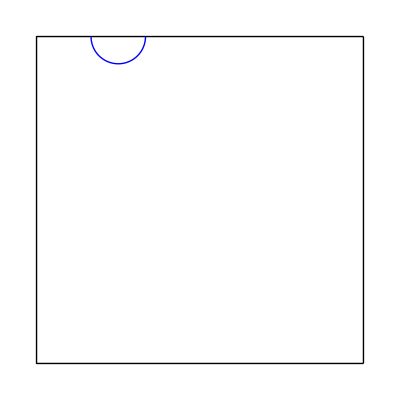
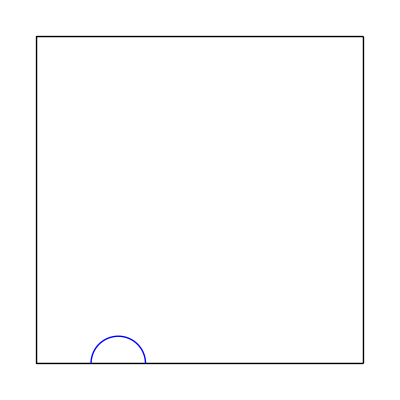
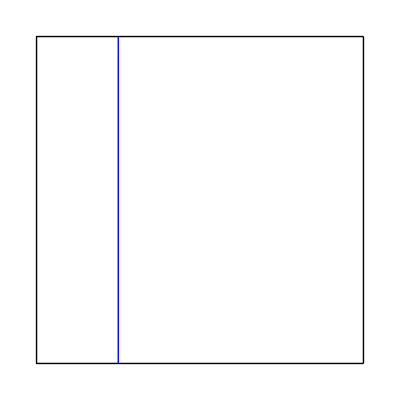
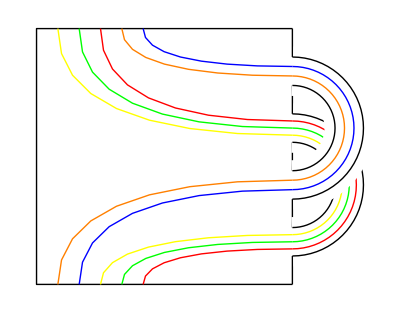
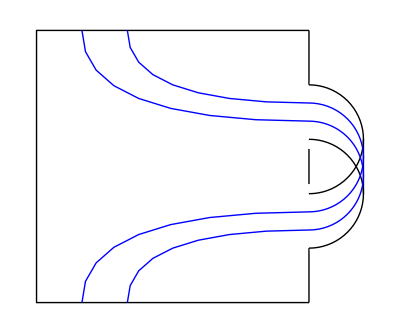
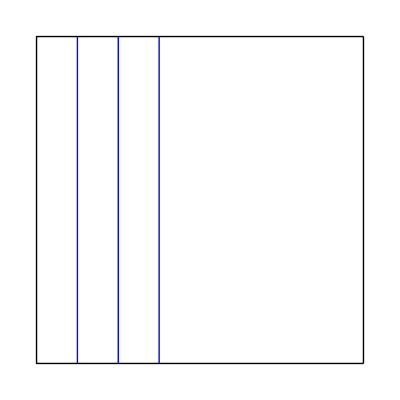
{-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
{Hompic[U],Hompic[V],Hompic[W],Hompiccol[Tor[2,3],CF],Hompic[Tw[2]],Hompic[w[3]]}
```

```mathematica
"Some sample calculations";
Eg1=MMult[{Tw[1],Tw[1],Tor[1,0]}];
A=MMult[{(Il[1]@*Ir[2])[V],(Il[2]@*Ir[1])[Tw[2]],Tw[5],Tor[5,0]}];
B=MMult[{Ir[2][Tw[1]],(Il[1]@*Ir[1])[Tw[1]],Il[2][Tw[1]]}];
BB=MMult[{Ir[4][Tw[1]],(Il[1]@*Ir[3])[Tw[1]],(Il[2]@*Ir[2])[Tw[1]],(Il[3]@*Ir[1])[Tw[1]],Il[4][Tw[1]]}];
CC=MMult[{Il[1][Tw[1]],Tor[1,1]}];
```

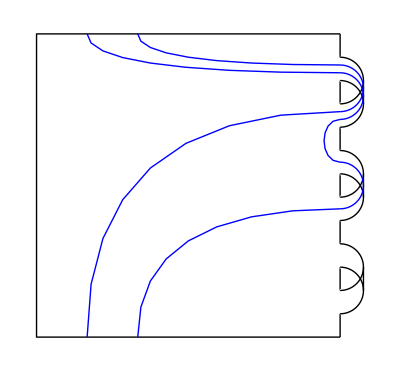
-Graphics-1

```mathematica
Hompic[(Hslide[3,"u"]@*Hslide[4,"d"]@*Hslide[5,"u"]@*Hslide[6,"d"]@*Hslide[4,"u"]@*Hslide[4,"d"]@*Htpe@*Hslide[4,"u"])[CC]]
```

```mathematica
Seq1=(Hslide[2,"u"]@*Hslide[3,"u"]@*Hslide[4,"u"]@*Hslide[5,"u"]@*Hslide[2,"d"]@*Hslide[1,"u"]@*Hslide[6,"u"]@*Hslide[3,"d"]@*Hslide[2,"d"]@*Hslide[8,"d"]@*Hslide[8,"d"]@*Hslide[4,"u"]@*Htpe@*Hslide[4,"u"]@*Htpe@*Hslide[6,"u"]);
SeqA=(Htpe@*Hslide[2,"u"]@*Hslide[6,"d"]@*Hslide[6,"d"]@*Htpe@*Hslide[7,"d"]@*Htpe@*Hslide[6,"u"]@*Htpe@*Seq1);
SeqB=(Htpe@*Hslide[2,"u"]@*Hslide[1,"u"]@*Htpe@*Hslide[4,"u"]@*Htpe@*Hslide[5,"u"]@*Hslide[2,"u"]@*Hslide[4,"u"]);
```

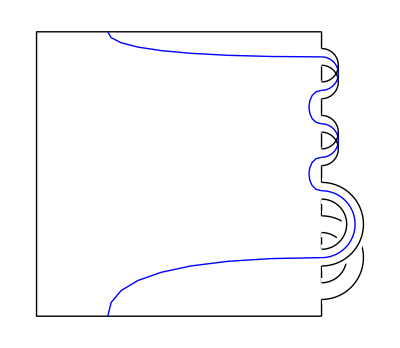
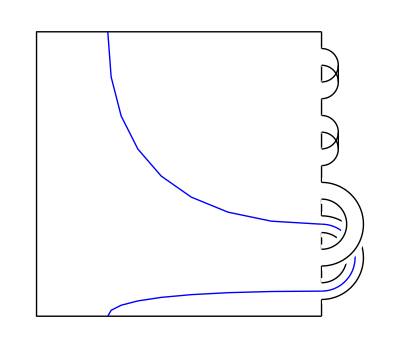
{-Graphics-1,-Graphics-1}

```mathematica
{Hompic[Eg1],Hompic[Seq1[Eg1]]}
```

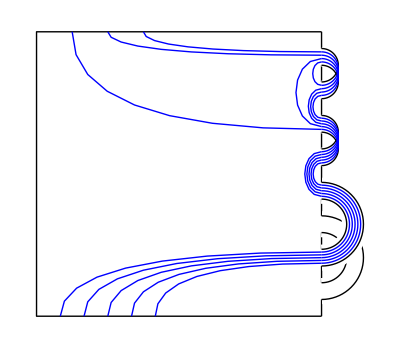
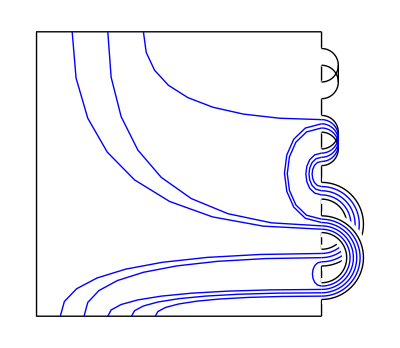
{-Graphics-1,-Graphics-1}

```mathematica
{Hompic[A],Hompic[SeqA[A]]}
```

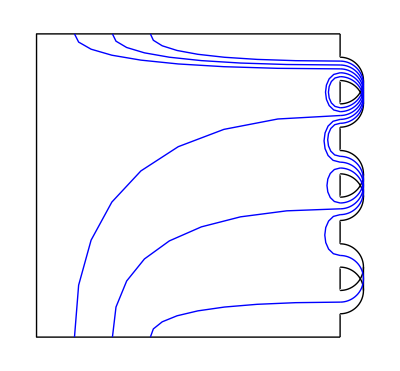
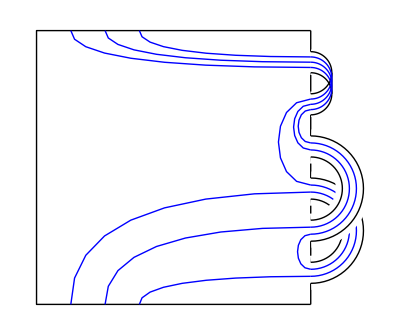
{-Graphics-1,-Graphics-1}

```mathematica
{Hompic[B],Hompic[SeqB[B]]}
```

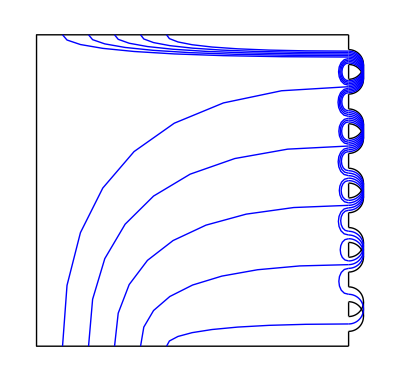
-Graphics-1

```mathematica
Hompic[BB]
```

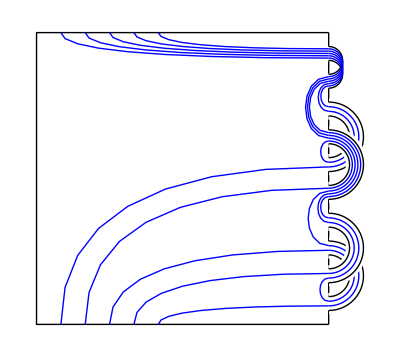
-Graphics-1

```mathematica
Hompic[(Tidy[1,5,8]@*Flip@*Htpe@*Hslide[5,"d"]@*Htpe@*Hslide[4,"d"]@*Htpe@*Hslide[3,"d"]@*Htpe@*Hslide[6,"d"]@*Htpe@*Hslide[4,"d"]@*Htpe@*Hslide[3,"d"]@*Htpe@*Hslide[2,"d"]@*Htpe@*Hslide[5,"d"]@*SeqB@*Flip@*SeqB)[BB]]
```

```mathematica
"Temperley-Lieb Generators";
u[n_,i_]:=Tens[w[i-1],Tens[Mult[U,V],w[n-i-1]]]
```

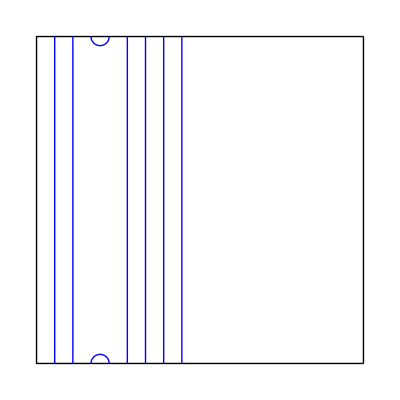
{-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
{Hompic[MMult[{u[8,3],u[8,4],u[8,3]}]],Hompic[MMult[{u[8,3],u[8,2],u[8,3]}]],Hompic[u[8,3]]}
```

```mathematica
Sfup[Data_]:=Module[{N},
N=Data[[2]];
Mult[Il[1][Data],Ir[N-1][U]]];
Sfdown[Data_]:=Module[{M},
M=Data[[3]];
Mult[Ir[M-1][V],Il[1][Data]]];
Sfrup[Data_]:=Module[{N},
N=Data[[2]];
Htpe[Mult[Ir[1][Data],Il[N-1][U]]]];
Sfrdown[Data_]:=Module[{M},
M=Data[[3]];
Htpe[Mult[Il[M-1][V],Ir[1][Data]]]
];
```

```mathematica
Hompiccol[(Htpe@*Hslide[4,"d"]@*Hslide[3,"u"]@*Hslide[4,"d"]@*Hslide[3,"u"]@*Sfup@*Sfup@*Sfup@*Sfup@*Sfrdown@*Sfrdown@*Sfrdown@*Sfrdown)[Gentor],CF]
```

Part::partd: Part specification Gentor⟦3⟧ is longer than depth of object.

Table::iterb: Iterator {j,1,-1+Gentor⟦3⟧} does not have appropriate bounds.

Join::heads: Heads Table and List at positions 1 and 2 are expected to be the same.

Part::partw: Part 3 of Htpe[Mult[{1,1+Gentor⟦3⟧,-1+Gentor⟦3⟧,0,{},Join[Table[{{0,j},{Plus[«2»],j}},{j,1,-1+Part[«2»]}],{{{0,Part[«2»]},{0,Plus[«2»]}}}]},Ir[1][Gentor]]] does not exist.

Table::iterb: Iterator {j,1,-1+Htpe[Mult[{1,1+Part[«2»],-1+Part[«2»],0,{},Join[Table[«2»],{«1»}]},Ir[1][Gentor]]]⟦3⟧} does not have appropriate bounds.

Join::heads: Heads Table and List at positions 1 and 2 are expected to be the same.

Part::partw: Part 3 of Htpe[Mult[{1,1+Htpe[Mult[{«6»},Ir[«1»][«1»]]]⟦3⟧,-1+Htpe[Mult[{«6»},Ir[«1»][«1»]]]⟦3⟧,0,{},Join[Table[{{0,j},{Plus[«2»],j}},{j,1,-1+Part[«2»]}],{{{0,Part[«2»]},{0,Plus[«2»]}}}]},Ir[1][Htpe[Mult[{1,1+Part[«2»],-1+Part[«2»],0,{},Join[Table[«2»],{«1»}]},Ir[1][Gentor]]]]]] does not exist.

Table::iterb: Iterator {j,1,-1+Htpe[Mult[{1,1+Part[«2»],-1+Part[«2»],0,{},Join[Table[«2»],{«1»}]},Ir[1][Htpe[Mult[«2»]]]]]⟦3⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Join::heads: Heads Table and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::partw: Part 3 of Htpe[Mult[{1,1+Htpe[Mult[{«6»},Ir[«1»][«1»]]]⟦3⟧,-1+Htpe[Mult[{«6»},Ir[«1»][«1»]]]⟦3⟧,0,{},Join[Table[{{0,j},{Plus[«2»],j}},{j,1,-1+Part[«2»]}],{{{0,Part[«2»]},{0,Plus[«2»]}}}]},Ir[1][Htpe[Mult[{1,1+Part[«2»],-1+Part[«2»],0,{},Join[Table[«2»],{«1»}]},Ir[1][Htpe[Mult[«2»]]]]]]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Simplify[Hompiccol[SortData[Gentor],CF]+Hompiccol[Sfup[Gentor],CF]+Hompiccol[Gentor,CF]+α*Hompiccol[Gentor,CF]+γ*Hompiccol[SortData[Gentor],CF]]
```

Part::partd: Part specification Gentor⟦6⟧ is longer than depth of object.

Part::partd: Part specification Gentor⟦1⟧ is longer than depth of object.

Part::partd: Part specification Gentor⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression Gentor cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Table::iterb: Iterator {i,0,1+2 Gentor⟦4⟧} does not have appropriate bounds.

Table::iterb: Iterator {k,1,Which[i==0,Gentor⟦2⟧,i==2 Gentor⟦4⟧+1,Gentor⟦3⟧,0<i<2 Gentor⟦4⟧+1,Select[5⟦Gentor⟧,Part[«2»]==i||Part[«2»]==i&]⟦1,4⟧]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Join::heads: Heads Table and List at positions 1 and 2 are expected to be the same.

ConnectedGraphComponents::graph: A graph object is expected at position 1 in ConnectedGraphComponents[Graph[Table[v[{i,k}],{k,1,Which[i==0,Gentor⟦2⟧,i==Times[«2»]+1,Gentor⟦3⟧,0<i<Times[«2»]+1,Select[Part[«2»],«1»&]⟦1,4⟧]},{i,0,1+2 Gentor⟦4⟧}],Join[Table[v[{Part[«3»],j}]<->v[{Part[«3»],Plus[«2»]}],{j,1,5⟦Gentor⟧⟦i,4⟧},{i,1,Gentor⟦4⟧}],{v[1]<->v[6],v[2]<->v[6]}]]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Graph[Table[v[{i,k}],{k,1,Which[i==0,Gentor⟦2⟧,i==Times[«2»]+1,Gentor⟦3⟧,0<i<Times[«2»]+1,Select[Part[«2»],«1»&]⟦1,4⟧]},{i,0,1+2 Gentor⟦4⟧}],Join[Table[v[{Part[«3»],j}]<->v[{Part[«3»],Plus[«2»]}],{j,1,5⟦Gentor⟧⟦i,4⟧},{i,1,Gentor⟦4⟧}],{v[1]<->v[6],v[2]<->v[6]}]]].

ConnectedGraphComponents::graph: A graph object is expected at position 1 in ConnectedGraphComponents[EdgeList[Graph[Table[v[{i,k}],{k,1,Which[i==0,Gentor⟦2⟧,i==Plus[«2»],Gentor⟦3⟧,0<i<Plus[«2»],Select[«2»]⟦1,4⟧]},{i,0,1+2 Part[«2»]}],Join[Table[v[{«2»}]<->v[{«2»}],{j,1,Part[«2»]⟦i,4⟧},{i,1,Gentor⟦4⟧}],{v[1]<->v[6],v[2]<->v[6]}]]]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[mmap[Graph[Table[v[{i,k}],{k,1,Which[i==0,Gentor⟦2⟧,i==Plus[«2»],Gentor⟦3⟧,0<i<Plus[«2»],Select[«2»]⟦1,4⟧]},{i,0,1+2 Part[«2»]}],Join[Table[v[{«2»}]<->v[{«2»}],{j,1,Part[«2»]⟦i,4⟧},{i,1,Gentor⟦4⟧}],{v[1]<->v[6],v[2]<->v[6]}]]]].

ConnectedGraphComponents::graph: A graph object is expected at position 1 in ConnectedGraphComponents[EdgeList[mmap[Graph[Table[v[{i,k}],{k,1,Which[Equal[«2»],Part[«2»],Equal[«2»],Part[«2»],Less[«3»],Part[«3»]]},{i,0,1+Times[«2»]}],Join[Table[v[«1»]<->v[«1»],{j,1,Part[«3»]},{i,1,Part[«2»]}],{v[«1»]<->v[«1»],v[«1»]<->v[«1»]}]]]]].

General::stop: Further output of ConnectedGraphComponents::graph will be suppressed during this calculation.

Join::heads: Heads List and Table at positions 1 and 2 are expected to be the same.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[mmap[fadd$11936[Graph[Table[v[{i,k}],{k,1,Which[Equal[«2»],Part[«2»],Equal[«2»],Part[«2»],Less[«3»],Part[«3»]]},{i,0,1+Times[«2»]}],Join[Table[v[«1»]<->v[«1»],{j,1,Part[«3»]},{i,1,Part[«2»]}],{v[«1»]<->v[«1»],v[«1»]<->v[«1»]}]]]]].

General::stop: Further output of EdgeList::graph will be suppressed during this calculation.

Join::heads: Heads Table and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::partw: Part 2 of mmap[fadd$11936[Graph[Table[v[{i,k}],{k,1,Which[1==Plus[«2»],Gentor⟦3⟧,0<i<Plus[«2»],Select[«2»]⟦1,4⟧]},{i,0,1+2 Part[«2»]}],Join[Table[v[{«2»}]<->v[{«2»}],{j,1,Part[«2»]⟦1,4⟧},{i,1,Gentor⟦4⟧}],{v[1]<->v[6],v[2]<->v[6]}]]]] does not exist.

Part::partw: Part 3 of fadd$11936[Graph[Table[v[{i,k}],{k,1,Which[1==1+Times[«2»],Gentor⟦3⟧,0<i<Times[«2»]+1,Select[Part[«2»],«1»&]⟦1,4⟧]},{i,0,1+2 Gentor⟦4⟧}],Join[Table[v[{Part[«3»],j}]<->v[{Part[«3»],Plus[«2»]}],{j,1,5⟦Gentor⟧⟦1,4⟧},{i,1,Gentor⟦4⟧}],{v[1]<->v[6],v[2]<->v[6]}]]] does not exist.

Part::partw: Part 2 of mmap[fadd$11936[Graph[Table[v[{i,k}],{k,1,Which[1==Plus[«2»],Gentor⟦3⟧,0<i<Plus[«2»],Select[«2»]⟦1,4⟧]},{i,0,1+2 Part[«2»]}],Join[Table[v[{«2»}]<->v[{«2»}],{j,1,Part[«2»]⟦1,4⟧},{i,1,Gentor⟦4⟧}],{v[1]<->v[6],v[2]<->v[6]}]]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

EdgeList::argt: EdgeList called with 0 arguments; 1 or 2 arguments are expected.

Table::nliter: Non-list iterator (bandcol[Gentor⟦4⟧,#1,CF]&)[{j,1,Gentor⟦4⟧}] at position 2 does not evaluate to a real numeric value.

EdgeList::argt: EdgeList called with 0 arguments; 1 or 2 arguments are expected.

Table::nliter: Non-list iterator (bandcol[Gentor⟦4⟧,#1,CF]&)[{j,1,Gentor⟦4⟧}] at position 2 does not evaluate to a real numeric value.

(1+α) Hompiccol[Gentor,CF]+Hompiccol[Mult[Il[1][Gentor],{1,-1+Gentor⟦2⟧,1+Gentor⟦2⟧,0,{},Join[{},Table[{{2 0+1,2+(-1+Gentor⟦2⟧)+1-j},{2 0,f$12222[2 0]+1-j}},{j,1,-1+Gentor⟦2⟧}],{{{1,1},{1,2}}}]}],CF]+-Graphics-Gentor⟦1⟧+γ -Graphics-Gentor⟦1⟧

```mathematica
SortData[Data_]:=Module[{L},
L=Length[Data[[6]]];

{Data[[1]],
Data[[2]],
Data[[3]],
Data[[4]],
Sort[Data[[5]]],
Sort[
Table[
Sort[Data[[6,i]]],{i,1,L}
]
]
}
]
```

```mathematica
TLeval[D1_+D2_,Colfn_]:=TLeval[D1,Colfn]+TLeval[D2,Colfn];TLeval[λ_*D_,Colfn_]/;FreeQ[λ,Pic[_]]:=λ*TLeval[D,Colfn];TLeval[λ_ D_,Colfn_]/;FreeQ[λ,Pic[_]]:=λ*TLeval[D,Colfn];
TLeval[Pic[{sc_,n_,m_,N_,BD_,CD_}],Colfn_]:=sc*Hompiccolnl[SortData[{1,n,m,N,BD,CD}],Colfn];
```

```mathematica
TLeval[a_**(b_+d_)**c_,Colfn_]:=TLeval[a**b**c+a**d**c,Colfn];
TLeval[a_**(b_+c_),Colfn_]:=TLeval[a**b+a**c,Colfn];
TLeval[(a_+b_)**c_,Colfn_]:=TLeval[a**c+b**c,Colfn];
```

```mathematica
TLeval[a_**(λ_*b_)**c_,Colfn_]/;FreeQ[λ,Pic[_]]:=λ*TLeval[a**b**c,Colfn];
TLeval[a_**(λ_ b_)**c_,Colfn_]/;FreeQ[λ,Pic[_]]:=λ*TLeval[a**b**c,Colfn];TLeval[a_**(λ_*b_),Colfn_]/;FreeQ[λ,Pic[_]]:=λ*TLeval[a**b,Colfn];
TLeval[a_**(λ_ b_),Colfn_]/;FreeQ[λ,Pic[_]]:=λ*TLeval[a**b,Colfn];
TLeval[(λ_*a_)**b_,Colfn_]/;FreeQ[λ,Pic[_]]:=λ*TLeval[a**b,Colfn];
TLeval[(λ_ a_)**b_,Colfn_]/;FreeQ[λ,Pic[_]]:=λ*TLeval[a**b,Colfn];
```

```mathematica
TLeval[Pic[D2_]**Pic[D1_],Colfn_]:=TLeval[Pic[(Deloop@*Htpe)[Mult[D2,D1]]],Colfn];
TLeval[Pic[D2_]**Pic[D1_]**A_,Colfn_]:=TLeval[Pic[(Deloop@*Htpe)[Mult[D2,D1]]]**A,Colfn];
```

```mathematica
Def[n_]:=(TLeval[nProduct[Array[Pic@*F_,n]],Colfn_]:=TLeval[Pic[MMult[F[Table[n+1-i,{i,1,n}]]]],Colfn])
```

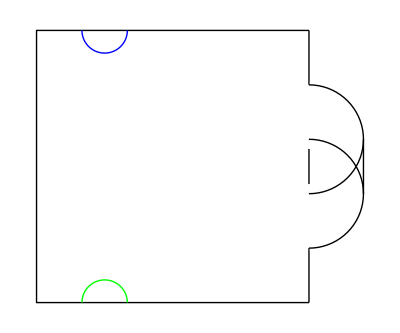
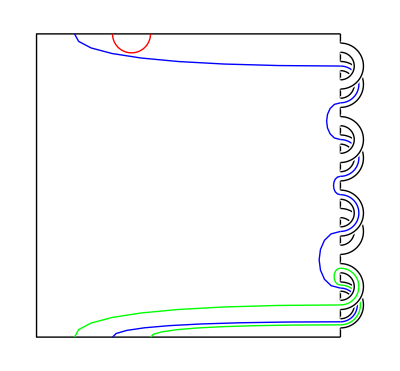
β -Graphics-+α -Graphics-

```mathematica
TLeval[Pic[u[3,2]]**Pic[Tor[1,2]]**Pic[Tor[1,2]]**Pic[u[3,1]]**Pic[Tor[1,2]]**Pic[Tor[1,2]]+Pic[u[2,1]]**Pic[Il[1][Tw[1]]]**Pic[u[2,1]],CF]
```

```mathematica
Rbow1={RGBColor[0, 1, 0],RGBColor[1, 0, 0],Purple,RGBColor[1, 0.5, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0]};
Rbow2={RGBColor[1, 0, 0],RGBColor[0, 1, 0],Purple,RGBColor[1, 0.5, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0]};
```

```mathematica
Hompiccolnl[Θ1,ClistF[Rbow1]]
```

Hompiccolnl[Θ1,ClistF[{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0]}]]

```mathematica
Hompiccolnl[Θ2,ClistF[Rbow2]]
```

Hompiccolnl[Θ2,ClistF[{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0]}]]

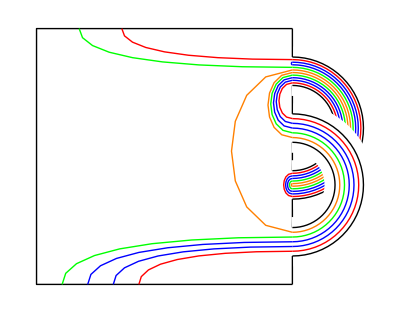

```mathematica
Hompiccolnl[(Hslide[3,"d"]@*Hslide[3,"u"])[Mult[(Sfdown@*Identity)[MMult[{(Ir[1]@*Il[2])[V],Tor[0,5]}]],(Ir[4])[U]]],CF]
```

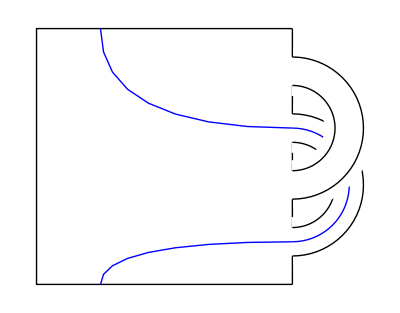
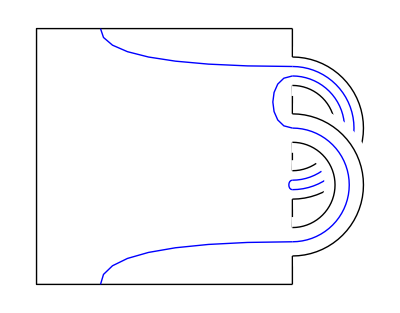

```mathematica
{Hompiccolnl[(Identity)[Tor[0,1]],CF],Hompiccolnl[(Hslide[3,"d"]@*Hslide[3,"u"])[Tor[0,1]],CF]}
```

### Temperley-Lieb Diagrams

A Temperley-Lieb diagram is something that looks like

```mathematica
D1={1,5,3,0,{},{{{1,1},{1,2}},{{0,1},{1,3}},{{0,3},{0,4}},{{0,2},{0,5}}}};
D2={1,3,7,0,{},{{{0,1},{1,1}},{{0,2},{1,6}},{{0,3},{1,7}},{{1,2},{1,3}},{{1,4},{1,5}}}};
```

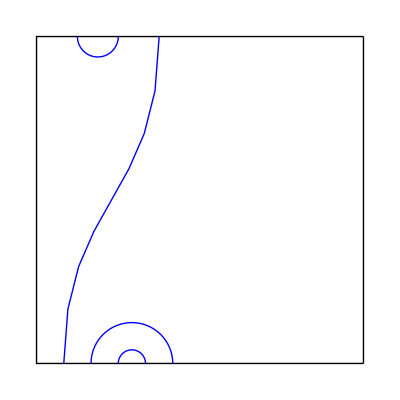
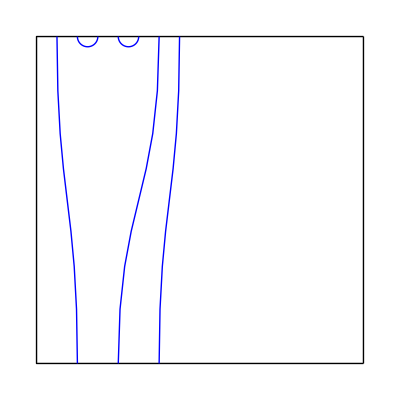
{-Graphics-1,-Graphics-1}

```mathematica
{Hompic[D1],Hompic[D2]}
```

We can mutliply by “stacking” pictures:

```mathematica
D3=Mult[D2,D1];
```

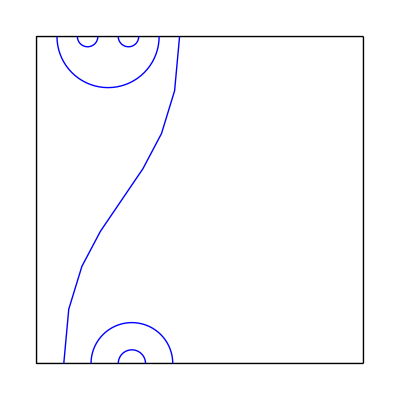
-Graphics-1

```mathematica
Hompic[D3]/.ImageSize->Small
```

We also allow ourselves to remove closed loops with a multiplicative parameter α:

```mathematica
{Hompic[U],Hompic[V]}
```

{-Graphics-1,-Graphics-1}

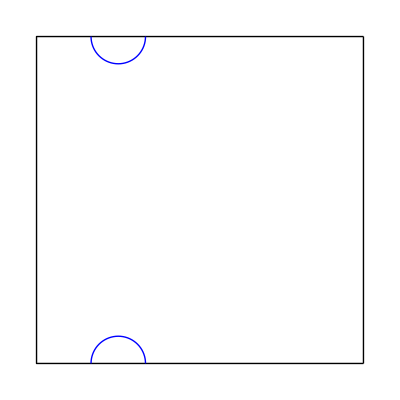
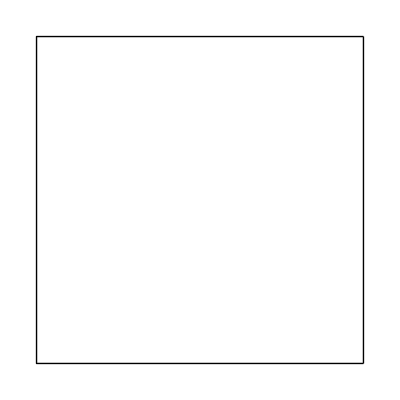
{-Graphics-1,-Graphics-α}

```mathematica
{Hompic[Mult[U,V]],Hompic[Mult[V,U]]}
```

### Surface Temperley-Lieb Diagrams

Instead of now drawing our diagrams inside a square frame which is a very simple surface, let us “play the game”  of drawing diagrams on different surface types (we will add the condition that they have one boundary component). We will do this by keeping the square frame and adding some handles on the right hand edge: the two simplest such surfaces are the following

```mathematica
T={1,0,0,2,{{0,1,3,0},{0,2,4,0}},{}};
M={1,0,0,1,{{1,1,2,0}},{}};
```

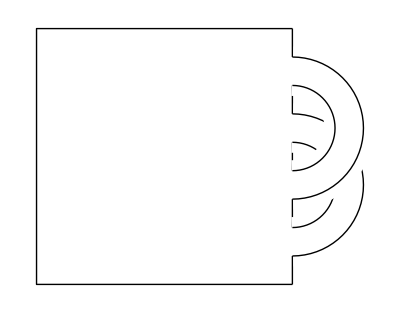
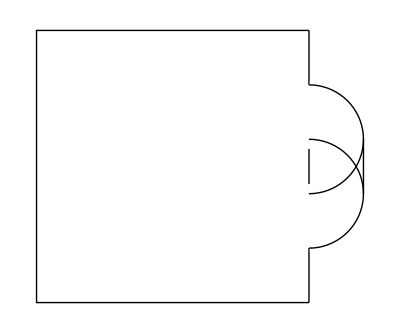
{-Graphics-1,-Graphics-1}

```mathematica
{Hompic[T],Hompic[M] }
```

Let us consider some possible diagrams:

```mathematica
S1=Mult[Ir[1][Il[1][V]],Il[1][Mult[Ir[1][Il[2][V]],Tor[2,3]]]];
```

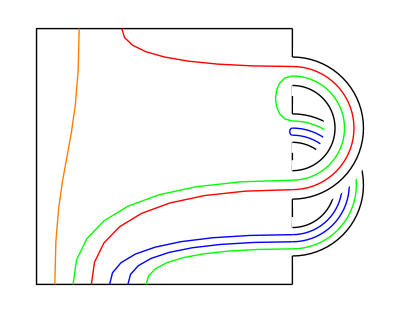

```mathematica
Hompiccolnl[S1,CF]
```

```mathematica
S2=(Htpe@*Hslide[3,"u"]@*Htpe@*Hslide[2,"u"])[Tens[Tor[0,3],Tw[3]]];
```

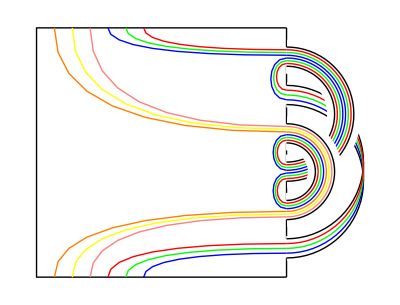

```mathematica
Hompiccolnl[S2,CF]
```

Pictures can get really complicated! We can also multiply by stacking pictures. For example, let us multiply the pictures above.

```mathematica
S3=Mult[S1,S2];
```

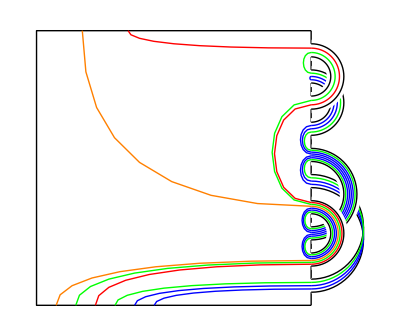

```mathematica
Hompiccolnl[S3,CF]
```

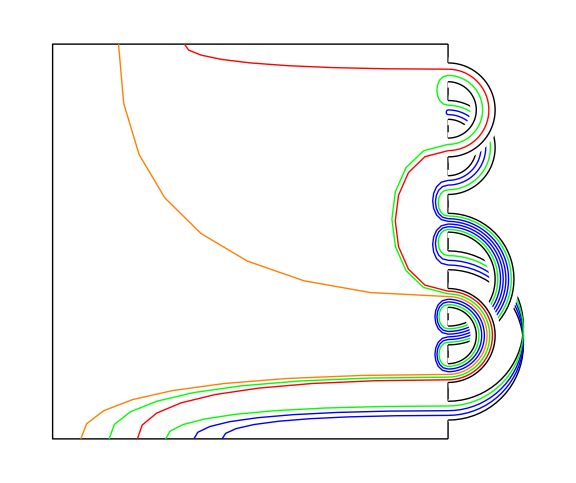

```mathematica
Show[%196,ImageSize->Large]
```

These seems out of control. A key notion however is that these pictures should be considered up to some equivalence - it shouldn’t matter what way the universe presents a surface to us. The equivalence is generated by isotopy and handlesliding.

#### Isotopy:

```mathematica
S4=Htpe[S3];
```

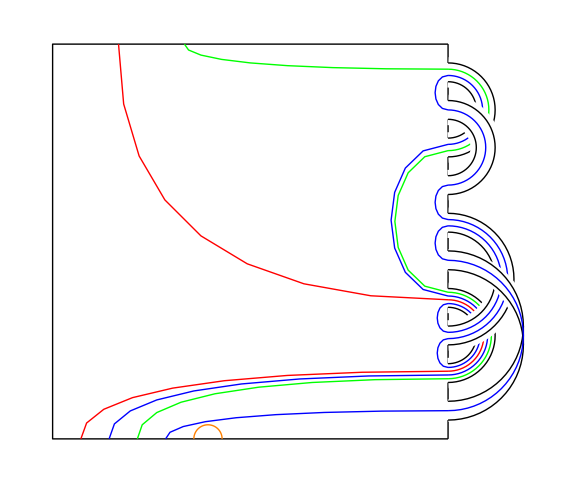

```mathematica
Show[Hompiccolnl[S4,CF],ImageSize->Large]
```

#### Handlesliding:

```mathematica
S5=(Htpe@*Hslide[7,"d"])[S4];
```

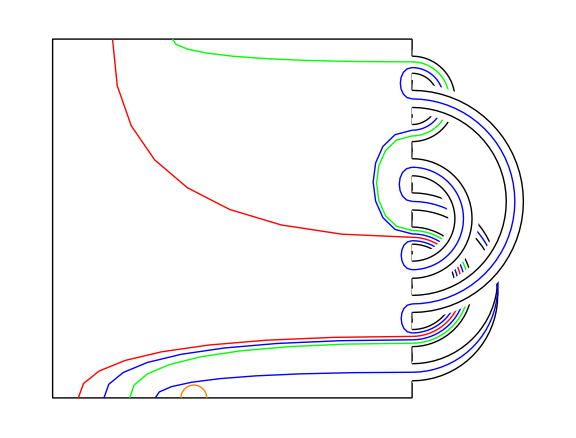

```mathematica
Show[Hompiccolnl[S5,CF],ImageSize-> Large]
```

```mathematica
S6=Tidy[1][S5];
```

```mathematica
S7=Tidy[2][S5];
```

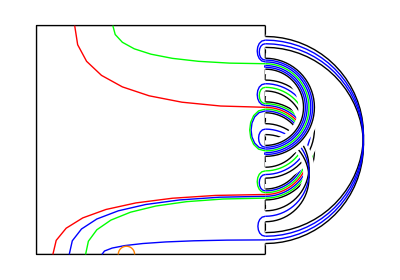

```mathematica
Hompiccolnl[(Hslide[5,"u"]@*Hslide[9,"u"]@*Hslide[6,"u"]@*Hslide[4,"d"]@*Hslide[8,"d"]@*Htpe@*Hslide[9,"d"]@*Htpe@*Hslide[8,"d"])[S6],CF]
```

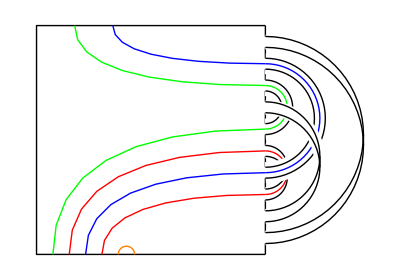

```mathematica
Hompiccolnl[S7,CF]
```